#### define a list:

```mathematica
alist={{a,b},{c,{d,e}}};
```

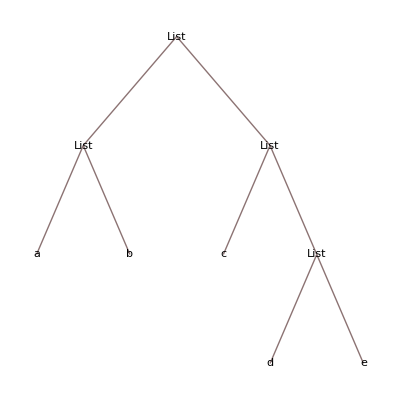

```mathematica
TreeForm[alist]
```

```mathematica
Level[alist,{-1}]
```

{a,b,c,d,e}

```mathematica
Level[alist,{-2}]
```

{{a,b},{d,e}}

## 1. Using only Apply and Plus, write a function that sums the rows of a matrix.

```mathematica
rowsum[m_]:=Apply[Plus,m,{1}]
```

```mathematica
rowsum[{{a,b},{c,d}}]
```

{a+b,c+d}